## extractor function

```mathematica
(*With[{dir="C:\\Users\\aliha\\Desktop\\",serial="A3",time="73",type="Nuc"},
fNames=dir<>serial<>" - "<>time<>"hrs";
ind=Flatten@StringCases[Import[fNames],x:DigitCharacter..:> FromDigits[x]];
ord=Ordering@ind;
indOrd=ind[[ord]];
(*masks=Import[dir<>serial<>" - "<>time<>"hrs\\Mask T"<>ToString[#]<>".tif"]&/@indOrd;*)
signal=Import[dir<>serial<>" - "<>time<>" hrs pp - "<>type<>".tif"][[indOrd]];
Print@Length@signal;
MapThread[
Export[dir<>"extracted images\\"<>time<>" hrs\\"<>serial<>"\\"<>type<>"\\"<>ToString[#2]<>".tif",#1]&,
{signal,indOrd}];
];*)
```

28

## preprocessing a single image

```mathematica
(* Trial on an image *)
```

```mathematica
sig=Import["C:\\Users\\aliha\\Desktop\\nuclear-marker-Reg.tif"];
```

```mathematica
ImageType[sig[[1]]]
```

Byte

```mathematica
Image[sig[[1]],ImageSize->Medium]
```

-Graphics-

```mathematica
mask = Import["C:\\Users\\aliha\\Desktop\\nuclear-marker-masks.tif"];
```

```mathematica
sigproc1=((ImageAdjust[TotalVariationFilter[BrightnessEqualize[#,Masking->ColorNegate@mask[[1]] ],0.5]]&@sig[[1]])*mask[[1]]);
```

```mathematica
sigproc2=((ImageAdjust[TotalVariationFilter[BrightnessEqualize@#,0.5]]&@sig[[1]])*mask[[1]]);
```

```mathematica
ImageAdjust@Image[#,ImageSize->Medium]&/@{sigproc1,sigproc2}
```

{-Graphics-,-Graphics-}

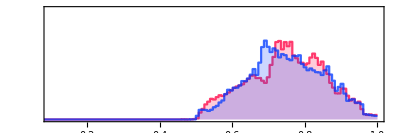

```mathematica
Show[ImageHistogram[First@#,PlotStyle->Last@#,PlotRange->{{0.1,1},Automatic}]&/@{{ImageAdjust@sigproc1,XYZColor[1,0,0,0.75]},{ImageAdjust@sigproc2,XYZColor[0,0,1,0.75]}}]
```

## preprocessing images

```mathematica
Clear@processImages;
processImages[dir_String,thresh_:0.5]:=Block[{NucsigDir,BsigDir,Nucsig,Bsig,maskDir,masks,
fileNames,order,NucsigProc,BsigProc,ind},

NucsigDir=dir<>"Nuc";
maskDir=dir<>"Mask";
ind=Flatten@StringCases[Import@maskDir,x:DigitCharacter..:> FromDigits[x]];
order=Ordering[ind];

Nucsig=Import[NucsigDir<>"\\*"];
Nucsig=ImageAdjust[#,{0,255},{0,255}]&/@Nucsig;

Print[ImageType[#]&@*First/@{Nucsig}];
masks=Import[maskDir<>"\\"<>#]&/@DeleteCases[Import[maskDir],"Thumbs.db"];

{masks,Nucsig}={masks[[order]],Nucsig[[order]]};

NucsigProc=MapThread[
ImageAdjust@TotalVariationFilter[BrightnessEqualize[#1,Masking->ColorNegate@#2],thresh]*#2&,{Nucsig,masks}
];
{Sort@ind,NucsigProc}
];
```

```mathematica
{ind,nucproc}=processImages["C:\\Users\\aliha\\Desktop\\phase separation\\"];
```

```mathematica
(* Export image sequence *)
```

```mathematica
MapThread[
Export["C:\\Users\\aliha\\Desktop\\phase separation\\Nuc-processed\\"<>ToString[#1]<>".tif",#2]&,{ind,ImageAdjust/@nucproc}
];
```